## Fancy Ralston Method

### Code

Code for a Fancy-Ralston step is below.   Taken from https://en.wikipedia.org/wiki/Bogacki%E2%80%93Shampine_method

```mathematica
FancyRalstonStep[f_,h_][{t0_,y0_}]:= Module[
{k1,k2,k3,k4,z1,z2,z3,w},
k1=f[t0,y0];
z1 = y0+1/2 * k1*h; 
k2 = f[t0+1/2 h, z1];
z2= y0 + 3/4*k2*h;
k3=f[t0+3/4 h, z2];
z3=y0 + h*(2/9 k1+1/3 k2 + 4/9 k3);
k4=f[t0+h,z3];
w=y0+h*(7/24 k1 + 1/4 k2 + 1/3 k3 + 1/8 k4);
{t0+h, w,z3}
]
```

### Synthetic ODE

Generate a “synthetic” ODE with a known solution

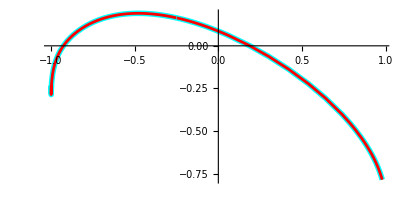

```mathematica
Clear[SynSol,ySol, f,t,y,g]
SynSol[t_]:= {Cos[t+Sin[t]], Sin[t] - Cos[Sin[t]-ArcTan[Cos[ t+ 2]+t]]}
g[t_,{y1_,y2_}]:={3.2 (y2+Sin[2 t]^2)Cos[t+y1], 2.3 t + Sin[t + y2]};
ff[t_]= Simplify[ SynSol'[t]-g[t,SynSol[t]]];
f[t_,y_]:=g[t,y]+ff[t]
t0=0.1; y0=SynSol[t0];
TMax=3.4;
ySol=NDSolveValue[ {y'[t]==f[t,y[t]],y[t0]==y0},y,{t,t0, t0+TMax}];
ParametricPlot[{ySol[t],SynSol[t]},{t, t0, t0+TMax},
PlotStyle->{{Cyan, Thickness[0.01]},{Red,Thickness[0.005]}}]
```

### Error Behavior

Lets look at the single steps we generate from the Fancy-Ralston (FR) procedure as a function of h.  One of the methods is much more accurate than the other! One is order 3 and the other is order 2.

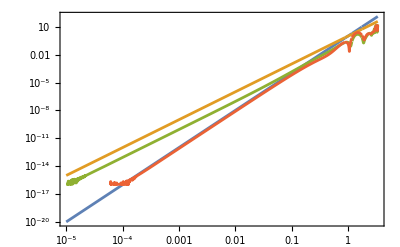

```mathematica
LogLogPlot[ {h^4,h^3,
Norm[FancyRalstonStep[f,h][{t0,y0}]⟦2⟧-SynSol[t0+h]],
Norm[FancyRalstonStep[f,h][{t0,y0}]⟦3⟧-SynSol[t0+h]]
},{h,10^-5,TMax},
GridLines->Automatic,Frame->True]
```

We know what it does!  We need to work out why the two pieces of information are useful.
We know when h is small that 
	||y[t0+h]-z||≈C_1 h^4 and ||y[t0+h]-w||≈C_2 h^3
so 
	||w-z||=||w-y[t0+h]+y[t0+h]-z||≤||w-y[t0+h]||+||y[t0+h]-z||
and
	||w-z||≤C_1 h^4+C_2 h^3≈C_2 h^3.
In words, the computable difference between the two predictions in FR scales like h^3 and provides an estimate for the error of the less accurate prediction w.

### Step Length Prediction

In practice, we want to make sure that our errors at each step are less than some tolerance. A typical tolerance is Tol=10^-7.

After an FR step of size h the error ||y-w||=err≈C_2 h^3.  If err>Tol then h was too large and it makes sense to try again with a scaled step γ h.   The expected error with a scaled step γ h is 
	(C_2(γ h))^3=C_2 h^3 γ^3=err γ^3
If all the estimates were exact the tolerance would be hit if   
	Tol=(C_2(γ h))^3=C_2 h^3 γ^3=err γ^3.
The step size control follows from 
	γ=(Tol/err)^(1/3) 
In practice the more cautious scheme 
	γ=(0.9Tol/err)^(1/3) 
is implemented that tries to satisfy
	0.9 Tol=err γ^3.

When||y-w||=err>Tol the step is bad: skip the update and try again with the smaller step size γ h where γ=(0.9Tol/err)^(1/3)<1.

When||y-w||=err≤Tol the step is good: take the best update z and try the next step with the adjusted step size γ h where γ=(0.9Tol/err)^(1/3)>1.

### Bogaki-Shampine ODE23

The Bogaki-Shampine pair is simply the code in FR with step-size control based on the above.

```mathematica
BogakiShampineStep[f_,Tol_][{t_,y_,h_}]:= Module[{tNew,w,z,err,γ},
{tNew,w,z}=FancyRalstonStep[f,h][{t,y}];
err=Norm[w-z];
γ=(0.9Tol/err)^(1/3);
If[ err≥Tol,
{t,y,γ h},
{tNew,z,γ h}]
]
```

```mathematica
Clear[SynSol,ySol, f,t,y,g]
SynSol[t_]:= {Cos[t+Sin[t]], Sin[t] - Cos[Sin[t]-ArcTan[Cos[ t+ 2]+t]]}
g[t_,{y1_,y2_}]:={3.2 (y2+Sin[2 t]^2)Cos[t+y1], 2.3 t + Sin[t + y2]};
ff[t_]= Simplify[ SynSol'[t]-g[t,SynSol[t]]];
f[t_,y_]:=g[t,y]+ff[t]
t0=0.1; y0=SynSol[t0];
TMax=3.4;
ySol=NDSolveValue[ {y'[t]==f[t,y[t]],y[t0]==y0},y,{t,t0, t0+TMax}];
ODESteps=50;
{Tol,h0}={10^-5,0.0001};
Data=NestList[BogakiShampineStep[f,Tol],{t0,y0,h0},ODESteps];
TabView[{
"Sol"->ParametricPlot[ySol[t],{t,t0, TMax},
Epilog->Point[Data⟦All,2⟧]],
"StepSize"->ListLogPlot[Data⟦All,3⟧,
PlotRange->All,
GridLines->Automatic,
Frame->True,
FrameLabel->{"i","h"}]
}
]
```

12